Select the parameter (.prm) file of the desired chromatogram. It is assumed that the chromatography files are in the same directory as the parameter file.

```mathematica
SystemDialogInput["FileOpen" , {"C:/Users/fskdm/Dropbox", {"Parameter Files"->{"*.prm"}}}]
```

```mathematica
pfile ="C:\\Users\\fskdm\\My PhD\\Projects\\2019_12_20_PhD_Last_Project\\2019_12_23_PAH_FAMEs\\Chromatograms\\RawData\\2020_02_19-140031.dat.prm"
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData\2020_02_19-140031.dat.prm

```mathematica
(*Extract the data directory:*)
filedir = FileNameJoin[ FileNameSplit[pfile][[1;;-2]]];

(*Import the parameters:*)
params = Import[pfile, "Lines"];

(*Create the data filename*)
file= FileNameJoin[
		{filedir
	,	FileNameSplit[
		StringSplit[                         
			params[[15]]                    (* Line 15 of the paramaters file contains the name of the data file *)
		][[3]]]                                        (* It is the third part of the line as separated by whitespace *)
		[[-1]]                                                 (* Select the last item on the list of the stringsplit *)
		}
	];(* Extract the filename *)
(* Show the result *)
Framed[TabView[{"Data"-> TableForm[{filedir, file}], "Parameters" -> params}]]
```

12

```mathematica
FrontEndTokenExecute["SaveRename", {StringJoin[file,".nb"]}]
```

```mathematica
(*data=BinaryReadList[file, {"Integer8"}~Join~Table["Real64", {17}], ByteOrdering->-$ByteOrdering];*)
```

```mathematica
Save[StringJoin[file,".wl"],data]
```

```mathematica
Get[StringJoin[file,".wl"]]
```

{{0,0.018,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1,660.011,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},15366,{3,850.231,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{4,850.231,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}
 |  |  |  |

```mathematica
Length[data[[1]]]
```

18

```mathematica
data[[-1,1]]=4
```

4

```mathematica
data[[-10;;-1]]//TableForm
```

2 | 9.196 | 303.411 | 294.599 | 5.21085 | 5.50061 | 2.03148×10^7 | 206930. | 644.864 | 656.883 | 0.0220184 | 627.232 | -0.0429077 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 683.15 | 623.15
2 | 9.253 | 303.412 | 294.585 | 5.16166 | 5.4481 | 2.03171×10^7 | 208259. | 644.98 | 656.972 | 0.0221222 | 627.118 | -0.0429077 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 683.15 | 623.15
2 | 9.275 | 303.415 | 294.59 | 5.15849 | 5.45049 | 2.03189×10^7 | 213887. | 644.955 | 656.936 | 0.0220337 | 628.231 | -0.0436035 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 683.15 | 623.15
2 | 9.308 | 303.414 | 294.59 | 5.19556 | 5.48733 | 2.03174×10^7 | 207641. | 645.025 | 657.018 | 0.021991 | 627.783 | -0.0432831 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 683.15 | 623.15
2 | 9.365 | 303.412 | 294.6 | 5.1443 | 5.42957 | 2.03172×10^7 | 207424. | 644.981 | 657. | 0.0224518 | 627.078 | -0.0429413 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 683.15 | 623.15
2 | 9.414 | 303.411 | 294.603 | 5.02812 | 5.30526 | 2.03201×10^7 | 210826. | 645.051 | 657.094 | 0.0221252 | 626.743 | -0.0432007 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 683.15 | 623.15
2 | 9.469 | 303.414 | 294.592 | 5.06372 | 5.34573 | 2.03196×10^7 | 212434. | 645.105 | 657.044 | 0.0225433 | 627.318 | -0.0430908 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 683.15 | 623.15
2 | 9.523 | 303.414 | 294.614 | 5.12949 | 5.41388 | 2.03196×10^7 | 210331. | 645.151 | 657.117 | 0.0221527 | 627.067 | -0.0432678 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 683.15 | 623.15
3 | 850.231 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 850.231 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
data
```

```mathematica
data[[1;;5]]//TableForm
```

0 | 0.018 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 660.011 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2 | 0.055 | 301.442 | 294.016 | 1.09927 | 0.745856 | 2.0252×10^7 | 327587. | 597.107 | 597.845 | 0.027243 | 303.179 | -0.0365845 | 2.0265×10^7 | 2.76769×10^7 | 623.15 | 623.15 | 257.817
2 | 0.081 | 301.446 | 294.041 | 1.09917 | 0.746338 | 2.02534×10^7 | 325979. | 597.104 | 597.844 | 0.0274994 | 303.253 | -0.0355988 | 2.0265×10^7 | 2.76769×10^7 | 623.15 | 623.15 | 264.75
2 | 0.104 | 301.446 | 294.01 | 1.09893 | 0.747153 | 2.02524×10^7 | 327463. | 597.055 | 597.756 | 0.025943 | 303.385 | -0.0375549 | 2.0265×10^7 | 2.76769×10^7 | 623.15 | 623.15 | 270.883

Plot the manifold temperatures:

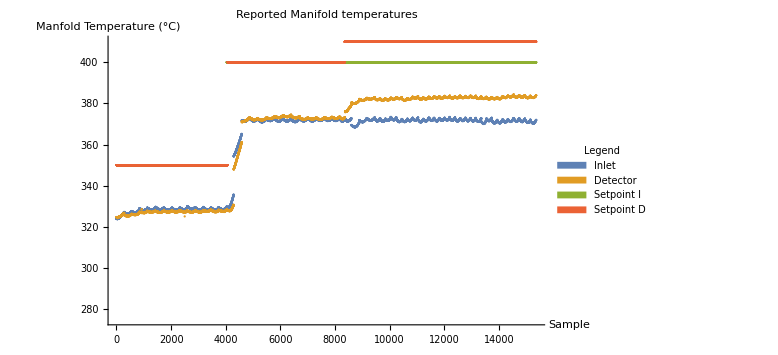

```mathematica
ListPlot[{data[[All,9]]-273.12, data[[All, 10]]- 273.12,data[[All, 16]]- 273.12,data[[All,17]]- 273.12}
, PlotRange->Automatic
(*, PlotLegends->{"Inlet","Detector","Setpoint I","Setpoint D"} *)
, PlotLegends->SwatchLegend[{"Inlet","Detector","Setpoint I","Setpoint D"} ,LegendLabel->"Legend",LegendFunction->(Framed[#,Background->LightBlue]&)]
, AxesLabel->{"Sample","Manfold Temperature (°C)"}
, ImageSize->Large
,PlotLabel->"Reported Manifold temperatures"

]
```

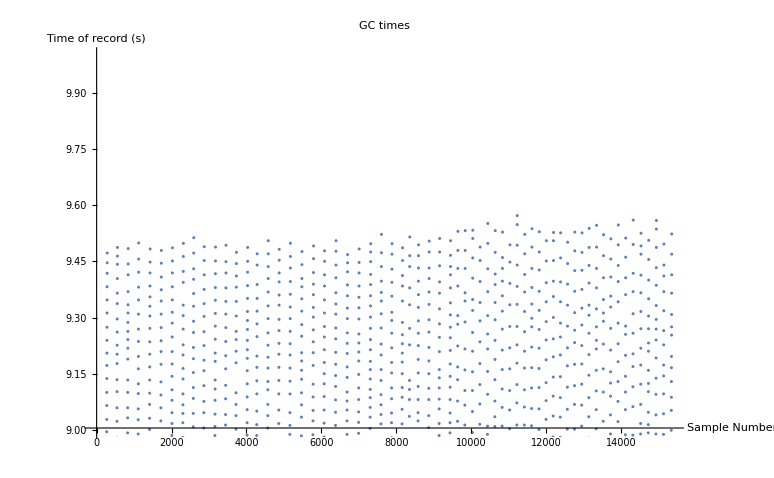

```mathematica
ListPlot[data[[All, 2]]
, PlotLabel->"GC times"
, AxesLabel->{"Sample Number", "Time of record (s)"}
, PlotRange->{9,10}
 ]
```

```mathematica
Position[data, _?#1[[2]]<#2[[2]]&]
```

{}

Just plot the temperatures:

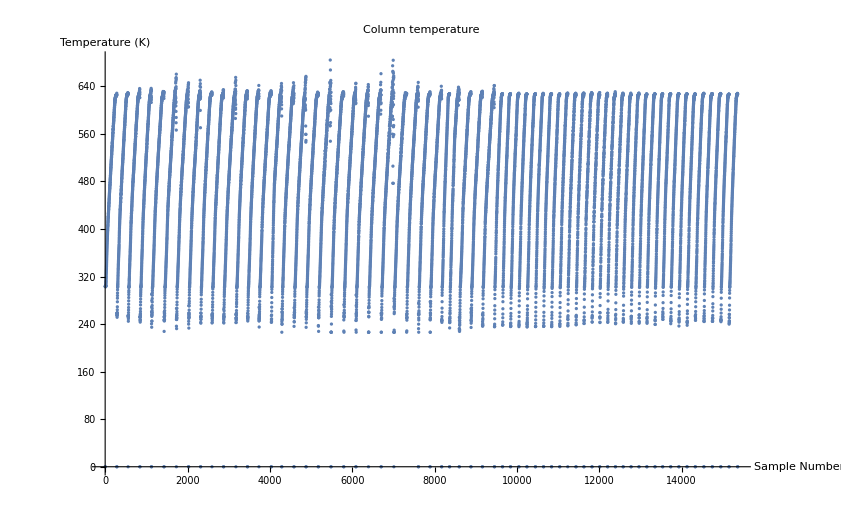

```mathematica
ListPlot[data[[All,12]]
, PlotLabel->"Column temperature"
, AxesLabel->{"Sample Number","Temperature (K)"}
 ]
```

```mathematica
values={"ID", "Time", "TAmbient", "Ttc", "Vb", "dV", "P1", "P2", "TInlet", "TOutlet", "Detector", "TColumn", "Vcol","P1 Setpoint", "P2 Setpoint", "TInlet Setpoint", "TOutlet Setpoint", "TColumn Setpoint"}
```

{ID,Time,TAmbient,Ttc,Vb,dV,P1,P2,TInlet,TOutlet,Detector,TColumn,Vcol,P1 Setpoint,P2 Setpoint,TInlet Setpoint,TOutlet Setpoint,TColumn Setpoint}

```mathematica
Join[{values}, {Range[18] } ]//TableForm
```

ID | Time | TAmbient | Ttc | Vb | dV | P1 | P2 | TInlet | TOutlet | Detector | TColumn | Vcol | P1 Setpoint | P2 Setpoint | TInlet Setpoint | TOutlet Setpoint | TColumn Setpoint
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18

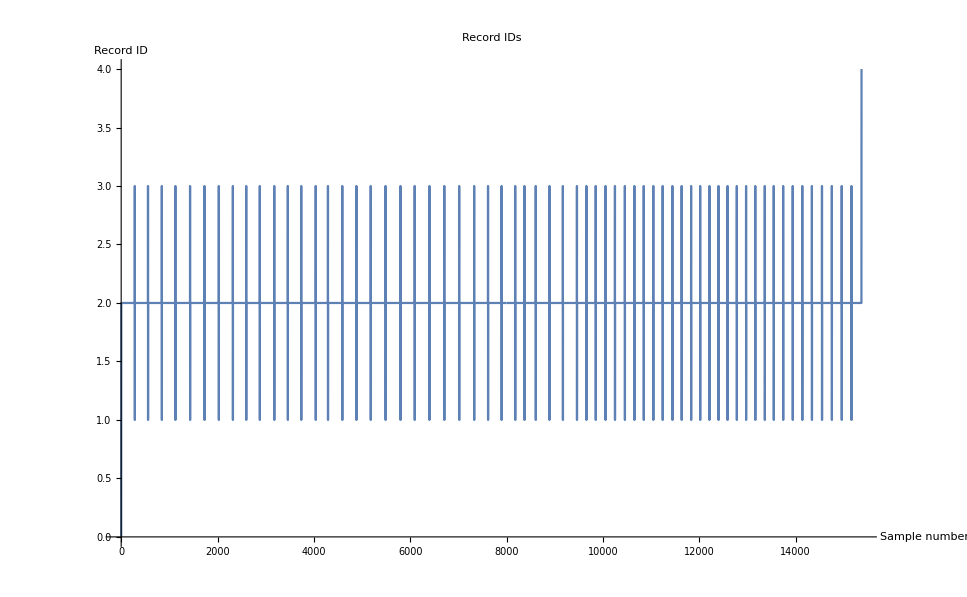

```mathematica
ListLinePlot[data[[All, 1]]
,PlotLabel->"Record IDs"
,AxesLabel->{"Sample number","Record ID"}
]
```

```mathematica
a3 = Position[data,{3,999.999,__}]//Flatten
```

{7328}

```mathematica
a1 = Position[data,{1,999.999,__}]//Flatten
```

{7329}

```mathematica
data[[a3,2]]=Mean[d1[[{25,27}]]]
```

735.466

```mathematica
Position[d1, 999.999]
```

{{26}}

```mathematica
Mean[d1[[{25,27}]]]
```

735.466

Split the data by ID. Turns the list into a list of lists.

```mathematica
data2 = Split[data, #1[[1]]==#2[[1]]&];
Column[{
Print["Data length: ",Length[data]]
,Print["data2 length: ",Length[data2]]
}]
```

Data length: 15370

data2 length: 191

```mathematica
data2[[All,1,1]]
```

```mathematica
data3= Select[data, #1[[1]]≠ 2&];
```

```mathematica
Length[data3]
```

128

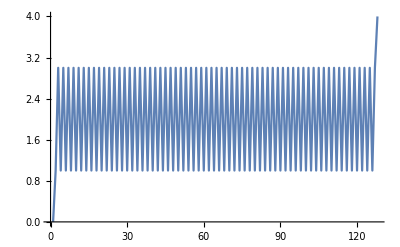

```mathematica
ListLinePlot[data3[[All,1]]]
```

Find the times of the GC runs, i.e. ID = 1. This  also counts the number of GC runs, i.e. the length of the first chromatographic dimension.

```mathematica
d1 = Select[data, #[[1]]==1&][[All, 2]];

Length[d1]
```

63

Check data integrity:
Number of GC runs (ID=2) + 2 per GC run (ID=1 and ID = 3) + ID=0 and ID=4

```mathematica
Length[d1]+Length[d1]*2 + 2
```

191

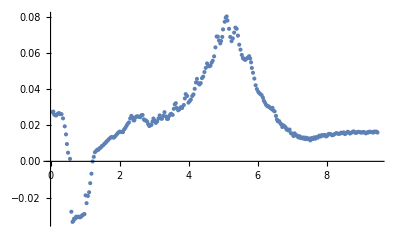

```mathematica
ListPlot[data2[[3,All,{2,11}]]]
```

```mathematica
Manipulate[
ListPlot[data2[[i,All,{2,11}]]
,PlotLabel->data2[[i,1,1]]
,Joined->True
 ]
,{i,1, Length[data2],1}
]
```

```mathematica
Array[#2+18*(#1-1)&,{3,18}]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36},{37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54}}

```mathematica
pattern = Array[ToExpression["x"<>ToString@(#2+18*(#1-1))<>"_"]&,{3,18}]
```

{{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_,x14_,x15_,x16_,x17_,x18_},{x19_,x20_,x21_,x22_,x23_,x24_,x25_,x26_,x27_,x28_,x29_,x30_,x31_,x32_,x33_,x34_,x35_,x36_},{x37_,x38_,x39_,x40_,x41_,x42_,x43_,x44_,x45_,x46_,x47_,x48_,x49_,x50_,x51_,x52_,x53_,x54_}}

```mathematica
TableForm[pattern]
```

1 | x2_ | x3_ | x4_ | x5_ | x6_ | x7_ | x8_ | x9_ | x10_ | x11_ | x12_ | x13_ | x14_ | x15_ | x16_ | x17_ | x18_
2 | x20_ | x21_ | x22_ | x23_ | x24_ | x25_ | x26_ | x27_ | x28_ | x29_ | x30_ | x31_ | x32_ | x33_ | x34_ | x35_ | x36_
3 | x38_ | x39_ | x40_ | x41_ | x42_ | x43_ | x44_ | x45_ | x46_ | x47_ | x48_ | x49_ | x50_ | x51_ | x52_ | x53_ | x54_

```mathematica
Position[data,PatternSequence[pattern[[1]]]]
```

{{2},{284},{557},{844},{1125},{1430},{2026},{2318},{2876},{3457},{4035},{4289},{4586},{4879},{5177},{5485},{5794},{6090},{6703},{7608},{7890},{8172},{8364},{8599},{8883},{9162},{9454},{9650},{9844},{10047},{10243},{10449},{10646},{10841},{11039},{11233},{11434},{11627},{11823},{12011},{12203},{12392},{12580},{12772},{12964},{13155},{13353},{13539},{13734},{13933},{14131},{14331},{14540},{14745},{14950},{15151},{15360}}

```mathematica
Position[data, PatternSequence[pattern[[2]]]]
```

{{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},15144,{15310},{15311},{15312},{15313},{15314},{15315},{15316},{15317},{15318},{15319},{15320},{15321},{15322},{15323},{15324},{15325},{15326},{15327},{15328},{15329},{15330},{15331},{15332},{15333},{15334},{15335},{15336},{15337},{15338},{15339},{15340},{15341},{15342},{15343},{15344},{15345},{15346},{15347},{15348},{15349},{15350},{15351},{15352},{15353},{15354},{15355},{15356},{15357},{15358}}
 |  |  |  |

```mathematica
Position[data, PatternSequence[pattern[[3]]]]
```

{{283},{843},{1124},{1429},{1729},{2025},{2317},{2594},{2875},{3175},{3456},{3734},{4034},{4288},{4585},{4878},{5176},{5484},{5793},{6089},{6394},{6702},{7011},{7607},{7889},{8171},{8363},{8598},{8882},{9161},{9453},{9649},{9843},{10046},{10242},{10448},{10645},{10840},{11038},{11433},{11626},{11822},{12010},{12202},{12391},{12579},{12771},{12963},{13154},{13352},{13538},{13733},{13932},{14130},{14330},{14539},{14744},{14949},{15150},{15359}}

```mathematica
Position[data, PatternSequence[pattern[[1]],pattern[[2]]]][[1;;10]]
```

Part::take: Cannot take positions 1 through 10 in {}.

{}⟦1;;10⟧

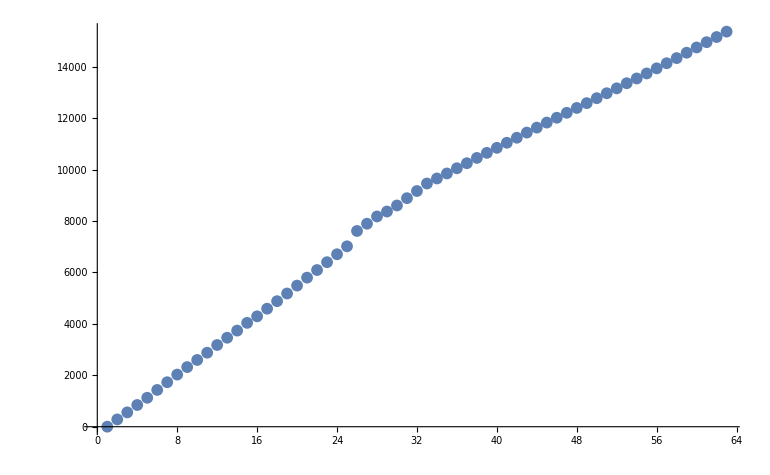

```mathematica
Position[data, pattern[[1]]]//Flatten//ListPlot
```

```mathematica
Manipulate[
TableForm[data[[i-1;;i+5]]]
, {i,Flatten[Position[data, pattern[[1]]|pattern[[3]]]]}
]
```

```mathematica
Join[{3,666.05},Table[0.,16]]
```

{3,666.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
data =Insert[data, Join[{3,999.999},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}], 7328];
```

```mathematica
data[[558]] = Join[{3,666.05},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}]
```

```mathematica
data[[11240,1]]=3
```

3

```mathematica
data[[-1,1]]=4
```

4

```mathematica
a=Position[data, pattern[[1]]]//Flatten
```

{2,284,558,845,1126,1431,1731,2028,2320,2597,2879,3179,3461,3739,4040,4294,4591,4884,5182,5490,5799,6095,6400,6709,7018,7329,7617,7899,8181,8373,8608,8892,9171,9463,9659,9853,10056,10252,10458,10655,10850,11048,11243,11444,11637,11833,12021,12213,12402,12590,12782,12974,13165,13363,13549,13744,13943,14141,14341,14550,14755,14960,15161,15370}

```mathematica
b =Position[data,pattern[[3]]|pattern0]//Flatten
```

{1,283,557,844,1125,1430,1730,2027,2319,2596,2878,3178,3460,3738,4039,4293,4590,4883,5181,5489,5798,6094,6399,6708,7017,7328,7616,7898,8180,8372,8607,8891,9170,9462,9658,9852,10055,10251,10457,10654,10849,11047,11242,11443,11636,11832,12020,12212,12401,12589,12781,12973,13164,13362,13548,13743,13942,14140,14340,14549,14754,14959,15160,15369}

```mathematica
a-b
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Length[%]
```

64

```mathematica
Length[a]==Length[b]
```

True

```mathematica
Manipulate[
Column[
{a=Position[data, pattern[[1]]]//Flatten;
b =Position[data,pattern[[3]]|pattern0]//Flatten;
a[[1;;i]]-b[[1;;i]]
,Row[{a[[i]],":",b[[i]]}]
}
]
, {i,1,Min[{Length[a],Length[b]}],1}
]
```

Part::partd: Part specification pattern⟦1⟧ is longer than depth of object.

Part::partd: Part specification pattern⟦3⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 58 in {}.

Part::partw: Part 58 of {} does not exist.

Part::partd: Part specification pattern⟦1⟧ is longer than depth of object.

Part::partd: Part specification pattern⟦3⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 58 in {}.

Part::partw: Part 58 of {} does not exist.

Part::partd: Part specification pattern⟦1⟧ is longer than depth of object.

Part::partd: Part specification pattern⟦3⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 58 in {}.

Part::partw: Part 58 of {} does not exist.

Part::partd: Part specification pattern⟦1⟧ is longer than depth of object.

Part::partd: Part specification pattern⟦3⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 58 in {}.

Part::partw: Part 58 of {} does not exist.

```mathematica
Manipulate[
TableForm[data[[i;;i+5]]]
, {i,6,Length[data]-5,1}
]
```

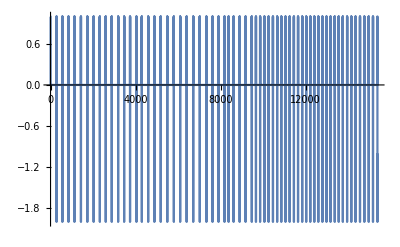

```mathematica
ListLinePlot[(RotateLeft[data][[All,1]]-data[[All,1]]), PlotRange->{All,All}]
```

```mathematica
Length[data2]
```

191

```mathematica
data2[[-1]]
```

{{4,850.231,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

Plot a GC run to see if looks sane:

```mathematica
Manipulate[
Show[
ListPlot[
	{Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
}
	, PlotLabel ->values[[dataset]]
, PlotRange->Automatic
,Joined->True
, PlotMarkers->Automatic
]
, Plot[220+4500./60.*t, {t, 0,12}]
,ImageSize -> Full]
	,{{gcrun,1,"GC Run"},1, Length[d1],1}
	,{{dataset,11, "Dataset"},1,18,1}
]
```

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[All]][[All,{2,12}]]//Length
```

63

```mathematica
Length[data2]
```

191

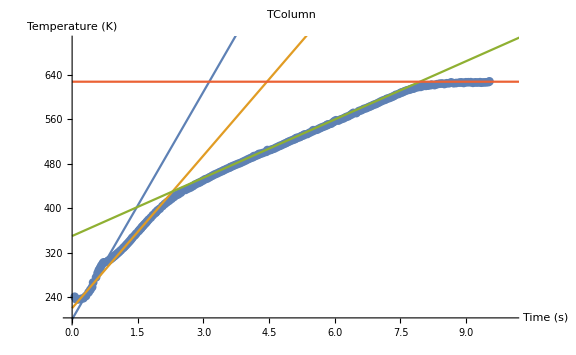

```mathematica
Show[
ListPlot[
	{Select[data2, #[[1]][[1]] ==2& ][[36]][[All,{2,12}]]
}
	, PlotLabel ->values[[12]]
, PlotRange->{{0,10},{200,700}}
,AxesLabel->{"Time (s)","Temperature (K)"}
,Joined->True
, PlotMarkers->Automatic
, ImageSize->Large
]
, Plot[{200+8200./60*t,220+5500./60*t,350+2100./60*t,355+273}, {t,0,12}]
]
```

Delete wrong data:

First identify index of wrong data

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[107]][[All,2]]
```

{0.033,0.056,0.079,0.114,0.137,0.159,0.182,0.207,0.23,0.252,0.274,0.297,0.319,0.341,0.365,0.387,0.409,0.448,0.471,0.494,0.516,0.538,0.561,0.583,0.622,0.645,0.667,0.69,0.714,0.737,0.759,0.782,0.821,0.845,0.867,0.889,0.923,0.946,0.968,0.991,1.032,1.054,1.078,1.118,1.141,1.163,1.186,1.215,1.238,1.261,1.283,1.317,1.34,1.363,1.385,1.407,1.441,1.463,1.485,1.525,1.548,1.571,1.593,1.616,1.638,1.661,1.683,1.705,1.745,1.767,1.789,1.819,1.842,1.864,1.888,1.91,1.932,1.955,1.977,1.999,2.025,2.047,2.069,2.091,2.113,2.136,2.158,2.18,2.202,2.242,2.265,2.287,2.309,2.332,2.355,2.377,2.399,2.422,2.444,2.466,2.488,2.511,2.534,2.557,2.579,2.619,2.641,2.664,2.686,2.718,2.74,2.763,2.785,2.809,2.831,2.854,2.875,2.898,2.92,2.942,2.964,2.987,3.009,3.032,3.055,3.078,3.119,3.142,3.165,3.187,3.215,3.24,3.263,3.285,3.323,3.349,3.371,3.393,3.432,3.455,3.478,3.5,3.534,3.556,3.578,3.618,3.64,3.663,3.686,3.711,3.734,3.757,3.779,3.817,3.84,3.863,3.885,3.913,3.936,3.958,3.981,4.017,4.04,4.063,4.085,4.117,4.14,4.162,4.184,4.21,4.234,4.257,4.279,4.301,4.341,4.364,4.386,4.411,4.439,4.461,4.483,4.515,4.538,4.56,4.583,4.613,4.636,4.658,4.68,4.712,4.734,4.757,4.779,4.813,4.836,4.86,4.882,4.911,4.933,4.955,4.978,5.,5.035,5.058,5.08,5.106,5.128,5.152,5.174,5.197,5.219,5.241,5.264,5.286,5.311,5.335,5.359,5.381,5.403,5.44,5.464,5.486,5.514,5.537,5.561,5.583,5.609,5.632,5.655,5.677,5.699,5.722,5.746,5.768,5.79,5.82,5.845,5.868,5.89,5.914,5.937,5.961,5.983,6.01,6.032,6.054,6.077,6.099,6.122,6.145,6.167,6.189,6.211,6.233,6.256,6.278,6.313,6.337,6.36,6.382,6.419,6.441,6.465,6.487,6.51,6.533,6.556,6.578,6.611,6.633,6.655,6.677,6.7,6.722,6.744,6.767,6.79,6.814,6.838,6.86,6.883,6.907,6.93,6.954,6.977,6.999,7.021,7.045,7.07,7.093,7.115,7.139,7.162,7.184,7.209,7.231,7.253,7.276,7.298,7.32,7.343,7.366,7.388,7.411,7.433,7.457,7.479,7.513,7.536,7.56,7.582,7.608,7.632,7.655,7.677,7.699,7.721,7.745,7.767,7.789,7.813,7.836,7.859,7.882,7.908,7.931,7.954,7.977,7.999,8.022,8.044,8.066,8.088,8.111,8.133,8.155,8.177,8.2,8.234,8.257,8.279,8.306,8.33,8.352,8.375,8.397,8.419,8.442,8.464,8.487,8.511,8.534,8.557,8.579,8.605,8.628,8.651,8.673,8.696,8.718,8.741,8.765,8.787,8.81,8.833,8.855,8.877,8.913,8.935,8.959,8.981,9.007,9.03,9.052,9.077,9.099,9.122,9.144,9.166,9.191,9.221,9.244,9.266,9.289,9.311,9.333,9.358,9.38,9.411,9.434,9.457,9.479,9.509,9.531,9.555,9.577,9.599,9.622,9.646,9.668,9.69,9.713,9.736,9.759,9.781,9.814,9.837,9.859,9.882,9.908,9.93,9.954,9.976,9.998,10.021,10.043,10.066,10.088,10.114,10.137,10.16,10.183,10.21,10.233,10.256,10.278,10.313,10.337,10.359,10.381,10.409,10.432,10.453,10.476,10.498,10.52,10.543,10.565,10.587,10.61,10.632,10.656,10.678,10.7,10.736,10.76,10.782,10.814,10.836,10.858,10.881,10.908,10.93,10.955,10.977,10.999,11.022,11.044,11.066,11.089,11.111,11.133,11.155,11.178,11.2,11.222,11.244,11.267,11.289,11.312,11.334,11.358,11.381,11.413,11.436,11.46,11.482,11.512,11.535,11.558,11.581,11.606,11.629,11.652,11.675,11.697,11.727,11.75,11.774,11.824,11.846,11.869,11.891,11.925,11.948,11.971,11.993,12.016,12.038,12.062,12.086,12.116,12.139,12.161,12.183,12.217,12.241,12.264,12.286,12.309,12.332,12.354,12.377,12.4,12.422,12.446,12.468,12.491,12.513,12.536,12.558,12.58,12.617,12.64,12.664,12.686,12.709,12.731,12.755,12.777,12.799,12.822,12.845,12.867,12.89,12.921,12.944,12.966,12.989}

Delete wrong data:

```mathematica
data2[[107*3+1+2]]=0
```

0

Check that data was deleted

```mathematica
data2[[109*3+1+2]][[-12;;-1]]
```

{{2,12.543,304.292,339.084,5.62898,6.11005,2.03211×10^7,-818256.,623.975,631.091,0.051535,629.374,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.565,304.293,339.085,5.62948,6.1097,2.03214×10^7,-818565.,624.021,631.109,0.0514587,629.225,-0.012323,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.588,304.294,339.097,5.62956,6.11065,2.03207×10^7,-817978.,624.073,631.129,0.0513306,629.371,-0.0124054,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.61,304.293,339.077,5.63014,6.10977,2.03209×10^7,-817792.,624.078,631.125,0.0511719,629.117,-0.0124908,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.636,304.292,339.096,5.5837,6.05612,2.03232×10^7,-815319.,624.035,631.075,0.051297,628.567,-0.0121246,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.658,304.291,339.077,5.55763,6.03091,2.03235×10^7,-816463.,624.128,631.165,0.0512878,629.088,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.681,304.291,339.077,5.55432,6.02879,2.03216×10^7,-816958.,624.1,631.165,0.0511505,629.339,-0.0126221,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.713,304.295,339.077,5.55583,6.0275,2.03211×10^7,-815350.,624.128,631.153,0.0510529,628.84,-0.012735,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.735,304.293,339.101,5.53895,6.01089,2.0324×10^7,-815195.,624.152,631.109,0.0510132,629.129,-0.0126862,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.758,304.293,339.094,5.53032,6.00199,2.03235×10^7,-815597.,624.228,631.211,0.0510376,629.21,-0.0126617,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.78,304.293,339.102,5.52975,6.00178,2.03237×10^7,-815319.,624.24,631.227,0.0511139,629.28,-0.0128387,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.81,304.292,339.11,5.53023,6.00126,2.03217×10^7,-815350.,624.219,631.232,0.0510315,629.102,-0.0127441,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15}}

```mathematica
Drop[data2, {42*3+1+2,
```

Examine data in relation with temperature:

```mathematica
Manipulate[
Show[
ListPlot[
{Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]], Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,12}]]}
, PlotLabel ->values[[dataset]]
,PlotRange->{{4,5},{0,5}}
,AxesLabel->{"Time (s)"}
, Joined->True
](* Ends ListPlot*)
, Plot[{-25+273,t*8000./60.-25+273, 60+2000./60*(t-0.6)+273,350+273},{t,0,12}]
, ListPlot[{{cur,0},{cur,10}}, Joined->True]
, ImageSize->Large
]
,{{gcrun,1,"GC Run"},1, Length[d1],1}
,{{dataset,11, "Dataset"},1,18,1}
,{{cur, 6, "Cursor"},0,12}
] (* Ends Manipulate *)
```

Print an SFC time to see if it looks sane

```mathematica
d1[[1]]
```

660.011

Create 3D values {t_r1,t_r2,det}

```mathematica
Clear[f]
```

```mathematica
f[x_, y_]:= {Map[Prepend[#,x]&,y]}
```

The number of GC runs:

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]]//Length
```

63

```mathematica
Length[d1]
```

63

```mathematica
data2d =Inner[f, d1, Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]], Join];
```

```mathematica
params //TableForm
```

GC column description:	Rxi-5Sil MS 0.250 mm x 1 m
SFC flow rate:	0.800
SFC temperature:	22.000
GC flow rate: 	99.000
Experiment title: 	PAH FAMEs
Sample name: 	10% Aromatics in diesel Total(TM) 50 ppm
Analysis type: 	Unknown
Concentration: 	9999.000
Operator name: 	DM
Detector sensitivity: 	1.0E-8
FID H2 flow rate: 	36.700
FID Air flow rate: 	300.000
SFC pressure: 	20265000 Pa
SFC dead time: 	660.000 s
File name: 	C:\SFC-GC\Data\2020_02_19-140031.dat
SFC gradient0:
Rate: 	0 $1 s^-1
Final:	0.000000 $1
Time:	900.000 s
GC gradient0:
Rate: 	0 $1 s^-1
Final:	243.150000 $1
Time:	0.000 s
GC gradient1:
Rate: 	267 $1 s^-1
Final:	393.150000 $1
Time:	0.000 s
GC gradient2:
Rate: 	33 $1 s^-1
Final:	623.150000 $1
Time:	2.000 s
GC idle temperature:	303.100000 Cdeg
GC purge temperature: 	343.150000 Cdeg
GC sampling temperature: 	263.150000 Cdeg
GC sampling time: 	3
GC load time: 	3
GC vent time: 	1

```mathematica
plot3d = ListPlot3D[
Flatten[data2d,1]
,PlotRange->{All, All, All}
,AxesLabel->{"SFC (s)", "GC (s)","Detector (V)"}
,PlotLabel->StringSplit[params[[6]], ":"][[2]]
,Mesh -> None

(*, ColorFunction->"BlueGreenYellow"*)
]
```

```mathematica
EmitSound[Sound[SoundNote[]]]
```

```mathematica
Show[plot3d, PlotRange->{{750,850},All,All}, ImageSize-> Full]
```

-Graphics3D-

```mathematica
Slider[Dynamic[opac]]
```

```mathematica
color = Dynamic[RGBColor[1,0,0,.5]]
```

```mathematica
Dynamic[i]
```

```mathematica
i=50
```

50

```mathematica
Slider[Dynamic[i],{1,Length[data2d],1}]
```

```mathematica
Show[plot3d, Graphics3D[{color,Line[data2d],Opacity[1], Black, Dynamic[Line[data2d[[i]]]]}],PlotRange->{{750,850},{0,5},{0,3}}, ImageSize->Full]
```

-Graphics3D-

Make a virtual SFC Chromatogram:

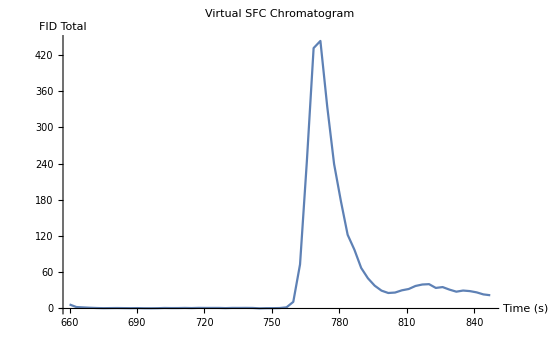

```mathematica
ListLinePlot[Partition[Riffle[d1,(Total[#]&/@data2d)[[All,3]]],2], PlotLabel->"Virtual SFC Chromatogram", AxesLabel->{"Time (s)","FID Total"}, PlotRange->{All, All}]
```

Create graphics for export to the thesis or publication:

```mathematica
exportgraphic = Show[
	plot3d
	,PlotLabel -> Style["FAMEs: Canola oil", Large, Bold, Black]
	, AxesStyle -> {Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				}
	,AxesLabel-> 
		{Style["SFC (s)", Large, Bold, Black]
		, Style[ "GC (s)",Large, Bold, Black]
		,Style[Rotate["Detector (V)", 90 Degree], Large, Bold, Black]
		}
	(*, ViewPoint->{10000,10000,10000} *)
	, ImageSize-> 1024
	, ViewPoint->vp
	
]
```

```mathematica
Export["C:\\Users\\fskdm\\My PhD\\Conferences\\Analitika 2018\\Poster\\images\\Canola.png",exportgraphic,Background->None, ViewPoint->vp]
```

C:\Users\fskdm\My PhD\Conferences\Analitika 2018\Poster\images\Canola.png

```mathematica
Show[
	plot3d
(*	,Graphics3D[{Red,Line[data2d]}] *)
     , PlotLabel -> "Mystery Oil"
	, PlotRange-> {All, All,{0,0.1}}
]
```

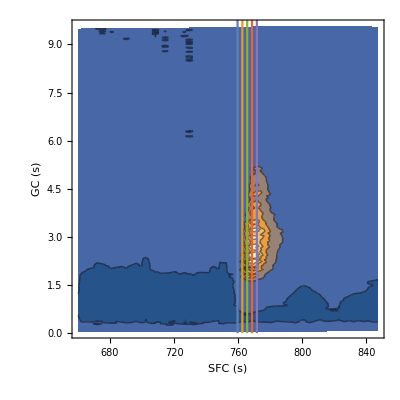

```mathematica
Show[
ListContourPlot[
Flatten[data2d,1]
, PlotRange->{All, All,All}
, AxesLabel->{"SFC (s)", "GC (s)"}
 ,InterpolationOrder->1
,ImageSize->Full]
,ListLinePlot[{{d1[[#]],0},{d1[[#]],10}}&/@{34,35,36,37,38}]
]
```

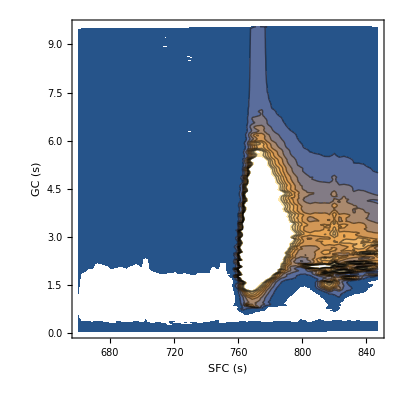

```mathematica
Show[contourplot, PlotRange->{{750,850}, All,{0.,3.}}]
```